```mathematica
Needs["NumericalCalculus`"];
```

## Precompute joint element

```mathematica
precomputeElement[EJ1_,EJ2_]:=Module[{t1,ϕ,ϕ1,int1,res},
t1=Monitor[Table[
res=Table[
FindMinimum[-EJ1 Cos[ϕ1]-EJ2 Cos[ϕ-ϕ1], {ϕ1, s1}][[1]]
,{s1,-π,π,π/3.}];
{ϕ, Min[res]}
,{ϕ,-2π,2.π,π/1000.}],ϕ];
Return[Interpolation[t1]];
(*Return[t1];*)
];

getEnergy[int1_, ϕ_]:=Module[{},
Return[int1[Mod[ϕ+2π,4π]-2π]];
];
getEnergyJJ[EJ_, ϕ_]:=Module[{},
Return[-EJ*Cos[ϕ]];
];
getEnergyLinInd[EL_, ϕ_]:=Module[{},
Return[EL/2 ϕ^2];
];
```

## Set up

In the unit of GHz

```mathematica
sf=10^-9/(2 π 1*10^-34);
Ic1=Quantity[0.7*10^-6,"Ampere"];
EJ1=sf*UnitConvert[(Quantity["FluxQuantum"]/(2π))Ic1 1/Quantity["Joule"],"SI"]
(*EJ2=α EJ1*)
(*EL=β EJ1*)
Subscript[H, arm][α_]:=Quiet[precomputeElement[EJ1,α EJ1]];
```

366.652

## Hamiltonian on the arms

```mathematica
αlist={0.5,1,2};
Subscript[listH, arm]=Monitor[Table[Subscript[H, arm][αlist[[i]]],{i,1,Length[αlist]}],αlist[[i]]];
```

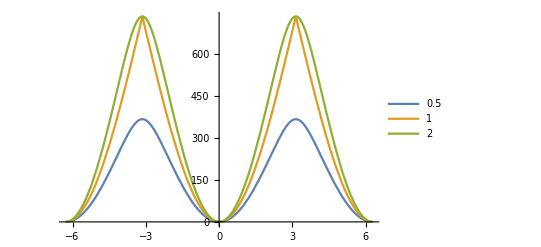

```mathematica
Subscript[xH, arm]=Table[getEnergy[Subscript[listH, arm][[i]],x]-getEnergy[Subscript[listH, arm][[i]],0],{i,1,Length[αlist]}];
Plot[Evaluate[Subscript[xH, arm]],{x,-2π,2π},PlotLegends->{"0.5","1","2"}]
```

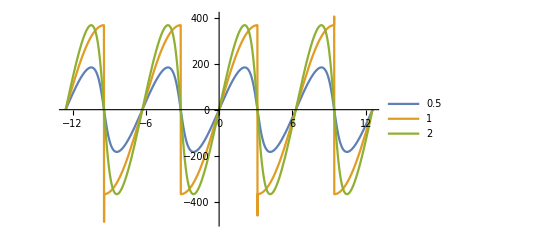

```mathematica
Plot[Evaluate[Table[D[Subscript[xH, arm][[i]],x]/.x->y,{i,1,Length[Subscript[listH, arm]]}]],{y,-4π,4π},PlotLegends->{"0.5","1","2"}]
```

## Total Hamiltonian

```mathematica
H[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_,ϕext_,Harm_,β_]:=
(getEnergy[Harm,ϕ1-ϕ2-ϕext/4]+getEnergy[Harm,ϕ2-ϕ3-ϕext/4]+ getEnergy[Harm,ϕ3-ϕ4-ϕext/4]+getEnergy[Harm,ϕ4-ϕ1-ϕext/4]-4getEnergy[Harm,0])+(getEnergyLinInd[β EJ1,ϕ1-ϕ5]+getEnergyLinInd[β EJ1,ϕ2-ϕ5]+getEnergyLinInd[β EJ1,ϕ3-ϕ5]+getEnergyLinInd[β EJ1,ϕ4-ϕ5]);
Hn[ϕ1_?NumericQ,ϕ2_?NumericQ,ϕ3_?NumericQ,ϕ4_?NumericQ,ϕ5_?NumericQ,ϕext_?NumericQ,Harm_,β_?NumericQ]:=(getEnergy[Harm,ϕ1-ϕ2-ϕext/4]+getEnergy[Harm,ϕ2-ϕ3-ϕext/4]+ getEnergy[Harm,ϕ3-ϕ4-ϕext/4]+getEnergy[Harm,ϕ4-ϕ1-ϕext/4]-4getEnergy[Harm,0])+(getEnergyLinInd[β EJ1,ϕ1-ϕ5]+getEnergyLinInd[β EJ1,ϕ2-ϕ5]+getEnergyLinInd[β EJ1,ϕ3-ϕ5]+getEnergyLinInd[β EJ1,ϕ4-ϕ5]);
```

#### Fix β, Varying α

```mathematica
ip=Table[RandomReal[{0,2π},4],20];
β=2;
```

```mathematica
Monitor[For[listt1={};j=1,j<=Length[αlist],j++,
Monitor[
t1=Table[
zt=Sort[Table[
res=Quiet[FindMinimum[Hn[ϕ1,ϕ2,ϕ3,ϕ4,0,ϕext,Subscript[listH, arm][[j]],β],{ϕ1,ip[[i,1]]},{ϕ2,ip[[i,2]]},{ϕ3,ip[[i,3]]},{ϕ4,ip[[i,4]]}]];
{res[[1]],ϕ1,ϕ2,ϕ3,ϕ4}/.res[[2]]
,{i,Length[ip]}]];
zt1={Flatten[{ϕext, zt[[1]]}]}
,{ϕext,-4π,4π,π/5}]
,ϕext];
listt1=Insert[listt1,t1,j]
],
αlist[[j]]]
```

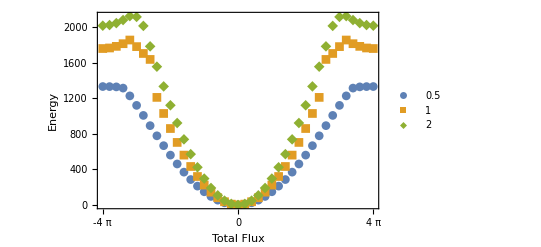

```mathematica
ListPlot[
Table[listt1[[i,All,1,{1,2}]],{i,1,Length[listt1]}],
 PlotMarkers->Automatic, Frame->True, FrameLabel->{"Total Flux","Energy"}, FrameTicks->{Automatic,{π Range[-8,8],None}},PlotLegends->{"0.5","1","2"}
]
```

```mathematica
Monitor[
For[listt2={};j=1,j<=Length[αlist],j++,
Monitor[
t2=Table[
{ϕext,ϕ1,ϕ2,ϕ3,ϕ4}=listt1[[j,i,1,{1,3,4,5,6}]];
ϕf=0;

h0=H[a (1/2 ϕy+1/2 ϕz+ϕw/4)+ϕ1,a(1/2 ϕx-1/2 ϕz+ϕw/4)+ϕ2,a(-1/2 ϕy+1/2 ϕz+ϕw/4)+ϕ3,a(-1/2 ϕx-1/2 ϕz+ϕw/4)+ϕ4,-a ϕw+ϕf, ϕext,Subscript[listH, arm][[j]],β];
{ϕext,
(ND[h0/.{a->1,ϕy->0,ϕz->0,ϕw->0},{ϕx,2},0])/2,
(ND[ND[ND[h0/.{a->1,ϕw->0},{ϕx,1},0],{ϕy,1},0],{ϕz,1},0]),
(ND[ND[h0/.{a->1,ϕz->0,ϕw->0},{ϕx,2},0],{ϕy,2},0])/4,
(ND[h0/.{a->1,ϕy->0,ϕz->0,ϕw->0},{ϕx,4},0])/24
}
,{i,Length[listt1[[j]]]}]
,listt1[[j,i,1,1]]];
listt2=Insert[listt2,t2,j]]
,αlist[[j]]]
```

```mathematica
Clear[x2,y2,x2y2,x4,x6,x4y2]
```

```mathematica
x2=Table[Interpolation[listt2[[i,All,{1,2}]]],{i,1,Length[αlist]}];
xyz=Table[Interpolation[listt2[[i,All,{1,3}]]],{i,1,Length[αlist]}];x2y2=Table[Interpolation[listt2[[i,All,{1,4}]]],{i,1,Length[αlist]}];x4=Table[Interpolation[listt2[[i,All,{1,5}]]],{i,1,Length[αlist]}];
```

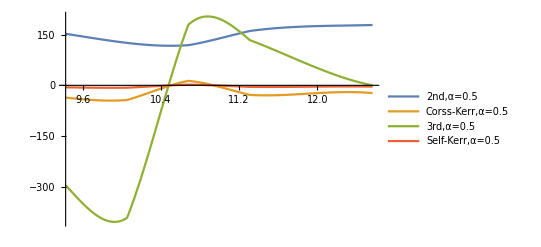

```mathematica
Plot[Evaluate[Table[xyz[[i]][x],{i,1,Length[αlist]}]],{x,-4π,4π},PlotLabel->"3rd",PlotLegends->{"α=0.5","α=1","α=2"}];

Plot[{x2[[1]][x],x2y2[[1]][x],xyz[[1]][x],x4[[1]][x]},{x,3π,4π},PlotLegends->{"2nd,α=0.5","Corss-Kerr,α=0.5","3rd,α=0.5","Self-Kerr,α=0.5"}]

Plot[Evaluate[Table[x4[[i]][x],{i,1,Length[αlist]}]],{x,-4π,4π},PlotLabel->"Self-Kerr",PlotLegends->{"α=0.5","α=1","α=2"}];

Plot[Evaluate[Table[x2y2[[i]][x],{i,1,Length[αlist]}]],{x,-4π,4π},PlotLabel->"Cross-Kerr",PlotLegends->{"α=0.5","α=1","α=2"}];
```